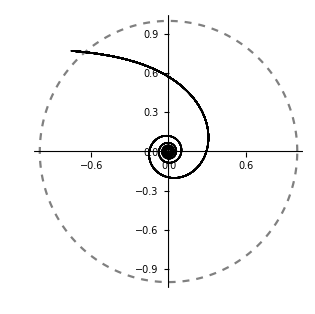

```mathematica
SetDirectory[NotebookDirectory[]];

Datos = Import["datos.dat"];
r=Datos[[All,2]];
phi=Datos[[All,3]];
listp2 = Transpose[{phi*180/Pi,r}];
Show[PolarPlot[1,{t,0,2*Pi},PlotStyle->{Gray,Dashed}],ListPolarPlot[listp2,PlotStyle->{Black}]]
```